```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
TT[mm_,x_]:=Piecewise[{{1/(√π),mm==0},{√(2/π)ChebyshevT[mm,x],mm>0}},0];
ψ[nn_,mm_,X_]:=Module[{x=X},
Return[Piecewise[{{2^((k+1)/2)TT[mm,2^(k+1)x-(2nn+1)],  nn/2^k≤  x && x< (nn+1)/2^k }},0]];
];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,0,2^k-1},{j,0,M}]];

γ[mm_]:=Piecewise[{{2,mm== 0},{1,mm≥ 1}}];

a[mm_,ii_]:=If[mm==0 && ii== 0,1,(-1)^ii 2^(2mm-2ii)(mm(2mm-ii-1)!)/(ii! (2mm-2ii)!)];
caputo[f_,{xx_,αα_},var_]:=Module[{nn=Ceiling[αα]},
If[!IntegerQ[αα],
Return[1/Gamma[nn-αα] Integrate[D[f/.xx->τ,{τ,nn}]/(var-τ)^(αα-nn+1),{τ,0,var},Assumptions->var>0]];
,
Return[D[f,{xx,nn}]/.Indeterminate->0];
];
];
g[t_]:=Module[{},
Return[Table[Simplify[caputo[yReal[t]⟦i⟧,{t,α⟦i⟧},t]-((f[t].(yReal[t]))⟦i⟧+Integrate[((t-s)^-β(K[t,s].(yReal[s])))⟦i⟧,{s,0,t},Assumptions->t>0])],{i,lenghtα}]];
];
Dstar[αα_,tt_]:=Module[{},
DαΨ=Flatten[Table[,{i,0,2^k-1},{j,0,M}]];
n=0;
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(is=0)^m 2^(k(m-is))a[m,is]caputo[tt^(m-is)Piecewise[{{1,0≤  tt && tt<   1/2^k}},0],{tt,αα},tt];
];
For[n=1,n≤2^k-1,n++,
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(is=0)^m ∑_(js=0)^(m-is) a[m,is]Binomial[m-is,js](-1)^(m-is-js)2^(k js)n^(m-is-js)caputo[tt^js Piecewise[{{1,n/2^k≤  tt && tt<   (n+1)/2^k}},0],{tt,αα},tt];
];
];
Return[Simplify[DαΨ]];
];
(**************************************)
(*gamma={0.85,0.90,0.95,1};*)
α={1,1,1};
f[t_]={{0,0,1},{1,0,0},{0,0,1}};
β={1/2,1/3,1/4};
K[t_,s_]={{s t,1,0},{0,1,1},{1,s^2 t,0}};
y0={0,0,0};
yReal[t_]={t(t-1),t^2,t^3};
k=1;M=4;
(*********************************)
lenghtα=Length[α];
c=Table[Subscript[CC, i ,j],{i,lenghtα},{j,2^k(M+1)}];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ANSWER[t_]=Table[-(c⟦i⟧.Dstar[α⟦i⟧,t])+g[t]⟦i⟧+(f[t].(c.Ψ[t]))⟦i⟧+Integrate[((t-s)^-β K[t,s].(c.Ψ[s]))⟦i⟧,{s,0,t},Assumptions->t>0],{i,lenghtα}];
```

```mathematica
(*chi=xx/.Sort[NSolve[{ChebyshevT[2^k(M+1)-1,2xx-1]==0,0≤ xx≤ 1},xx]]*)
(*
{0.006155829702,0.05449673791,.2730047501,.4217827675,.5782172325,.7269952499,.9455032621,.9938441703,.1464466095,.8535533905}*)
chi=Sort[N[Round[{.5000000000,0.007596123494,.1786061952,.3289899283,.6710100717,.8213938048,.9924038765,0.0669872980,0.9330127020},10^-12],10]]
```

{0.007596123494,0.066987298,0.1786061952,0.3289899283,0.5,0.6710100717,0.8213938048,0.933012702,0.9924038765}

```mathematica
ans=Flatten[Table[Simplify[ANSWER[chi⟦i⟧]],{i,Length[chi]}]];
```

```mathematica
ans0=c.Ψ[0]-y0;
ANSWERC=Simplify[Join[ans0,ans]];
Cc=Flatten[Flatten[c]/.NSolve[ANSWERC==0,Flatten[c]]];

yt[t_]=Simplify[Partition[Cc,2^k(M+1)].Ψ[t]];
```

```mathematica
ScientificForm[yt[t]]
```

{Piecewise[{{0., t≥1||t<0}, {3.46945×10^-17-1. t+1. t^2+(2.05094×10^-15) t^3-(1.65262×10^-15) t^4, 0≤t<1/2}, {1.01197×10^-13-1. t+1. t^2-(1.51039×10^-13) t^3+(6.25105×10^-14) t^4, True}}],Piecewise[{{0., t≥1||t<0}, {-5.77316×10^-14+(2.16716×10^-13) t+1. t^2+(1.44472×10^-13) t^3-(3.09616×10^-14) t^4, 1/2≤t<1}, {3.46945×10^-18+(3.33067×10^-16) t+1. t^2+(1.65327×10^-14) t^3-(2.24151×10^-14) t^4, True}}],Piecewise[{{0., t≥1||t<0}, {3.46945×10^-17-(1.38778×10^-16) t+(1.74248×10^-15) t^2+1. t^3+(1.37472×10^-14) t^4, 0≤t<1/2}, {7.77156×10^-15-(1.82521×10^-13) t+(2.63345×10^-13) t^2+1. t^3+(6.97499×10^-14) t^4, True}}]}

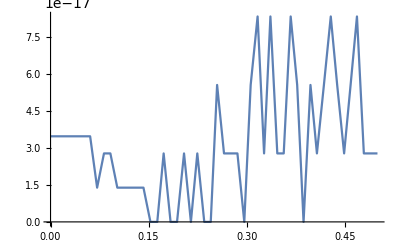

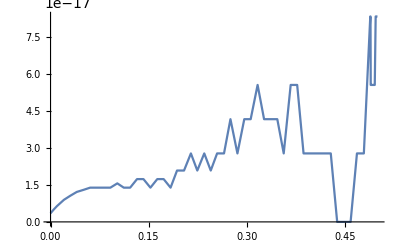

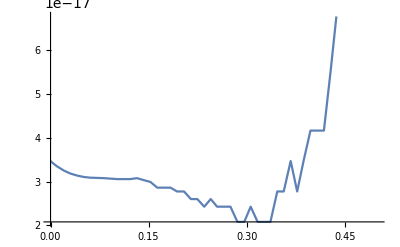

```mathematica
Plot[{Abs[yt[t]⟦1⟧-yReal[t]⟦1⟧]},{t,0,0.5},PlotLegends->Automatic,PlotRange->Full,PlotRange->1]
Plot[{Abs[yt[t]⟦2⟧-yReal[t]⟦2⟧]},{t,0,0.5},PlotLegends->Automatic,PlotRange->Full]
Plot[{Abs[yt[t]⟦3⟧-yReal[t]⟦3⟧]},{t,0,0.5},PlotLegends->Automatic]
```